```mathematica
两个圆线圈的等势线分布
```

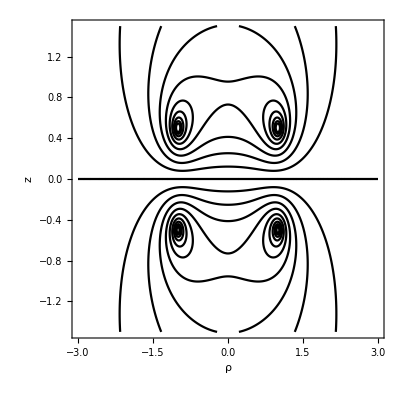

```mathematica
d=1;V0[z_,ρ_,R_]:=
(2EllipticK[-(2R*ρ)/(z^2+(R-ρ)^2)])/(√(z^2+(R-ρ)^2))+(2EllipticK[(2R*ρ)/(z^2+(R+ρ)^2)])/(√(z^2+(R+ρ)^2));
V1[z_,ρ_,R_]:=V0[z-d/2,ρ,R];
V2[z_,ρ_,R_]:=-V0[z+d/2,ρ,R];
V[z_,ρ_,R_]:=V1[z,ρ,R]+V2[z,ρ,R];
ContourPlot[V[z,ρ,1],{ρ,-3,3},{z,-1.5,1.5},
PlotPoints->100,ContourShading->False,
FrameLabel->{"ρ","z"},Contours->20,
ContourStyle->Thickness[0.004],
AxesStyle->Thickness[0.003]]
Clear[R,d,z,ρ,V,V0,V1,V2]
```